```mathematica
(* imports *)
images=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\C10 - cropped.tif"][[1;;160]];
masks1=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\C10 - masks.tif"][[1;;160]];
```

```mathematica
mask1=masks1[[125]];
```

```mathematica
masks2=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\D11 - masks.tiff"][[;;160]];
```

```mathematica
mask2=masks2[[-1]];
```

```mathematica
masks3=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\F10 - masks.tiff"];
```

```mathematica
mask3=masks3[[-1]];
```

```mathematica
(*m1 is reference to which other images need to be aligned to*)
```

```mathematica
(m1=ImagePad[mask1,{{67,68},{69,69}}])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
(m2=ImagePad[ImageRotate[mask2,-2.2Pi/5],{{55,55},{36,36}}])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
(m3=ImageRotate[mask3,-Pi/4])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
SameQ@@ImageDimensions/@{m1,m2,m3}
```

True

```mathematica
{HighlightImage[m1,m2,ImageSize->Small],HighlightImage[m1,m3,ImageSize->Small]}
```

{-Graphics-,-Graphics-}

```mathematica
(align1=ImageAlign[m1,m2,Method->"MeanSquareGradientDescent",
TransformationClass->"Affine",Background->0])//Image[#,ImageSize->Small]&
```

-Graphics-

```mathematica
(align2=ImageAlign[m1,m3,Method->"MeanSquareGradientDescent",
TransformationClass->"Affine",Background->0])//Image[#,ImageSize->Small]&
```

-Graphics-

```mathematica
HighlightImage[m1,{Red,align1,Blue,align2},ImageSize->200]
```

-Graphics-

```mathematica
interpBoundary[img_,div_]:=Module[{ℛ,polygon,t,interp,sub},
ℛ=ImageMesh[img,Method->"Exact"];
polygon=Append[#,First@#]&@MeshCoordinates[ℛ][[ MeshCells[ℛ,2][[1,1]] ]];t=Prepend[Accumulate[Norm/@Differences[polygon]],0.];interp=Interpolation[Transpose[{t,polygon}],InterpolationOrder->1,PeriodicInterpolation->True];sub=Subdivide[interp[[1,1,1]],interp[[1,1,2]],div];interp[sub]
];
```

```mathematica
interpPeri1=interpBoundary[m1,400];
interpPeri2=interpBoundary[m2,400];
interpPeri3=interpBoundary[m3,400];
```

```mathematica
{err1,transF1}=FindGeometricTransform[interpPeri1,interpPeri2,Method->"FindFit",TransformationClass->"Affine"]
```

{4.21984,TransformationFunction[(1.14388 | -0.127477 | -3.37842
0.265198 | 1.00838 | -53.0188
0. | 0. | 1.)]}

```mathematica
{err2,transF2}=FindGeometricTransform[interpPeri1,interpPeri3,Method->"FindFit",TransformationClass->"Affine"]
```

{3.55422,TransformationFunction[(1.06194 | -0.0152824 | -14.5293
0.122795 | 1.01339 | -27.617
0. | 0. | 1.)]}

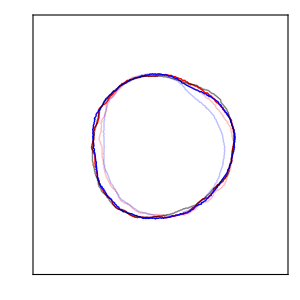

```mathematica
Graphics[
{{Thick,Red,Opacity[0.25],Line@interpPeri3},{Red,Thick,Line[transF2@interpPeri3]},
(*{GrayLevel[0.4],Arrowheads[Small],Arrow[{#,transF2@#}&/@interpPeri2]},*)
{Thick,Blue,Opacity[0.25],Line@interpPeri2},{Thick,Blue,Line[transF1@interpPeri2]},
{Thick,Opacity[0.5],Black,Line@interpPeri1}},PlotRange->{{0,382},{0,382}},ImageSize->300,
Frame->True,FrameTicks->False
]
```

```mathematica
(* till above we have a transformation matrix (affine transformation class) obtained from image masks that we can use to transform the points from one image to another *)
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim1.mx";
res1=sim;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim3-filter20.mx";
res2=sim;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim2.mx";
res3=sim;
```

```mathematica
meanFlowField[flowfield_]:=Normal@GroupBy[Flatten[Thread/@flowfield,1],First->Last,Mean]/.Rule-> List;
```

```mathematica
{meanflow1,meanflow2,meanflow3}=meanFlowField/@{res1,res2,res3};
```

```mathematica
(* we have mean flow fields for all the three aggregates *)
```

```mathematica
{pts1,vec1}=Transpose@meanflow1;
{pts2,vec2}=Transpose@meanflow2;
{pts3,vec3}=Transpose@meanflow3;
```

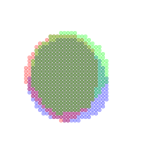

```mathematica
Graphics[{Opacity[0.3],Blue,Point@pts1,Red,Point@pts2,Green,Point@pts3},PlotRange->{{0,280},{0,280}},ImageSize->150]
```

```mathematica
{rotatedm1,rotatedm2,rotatedm3}=ImageRotate[#,Pi/2]&/@{m1,m2,m3};
```

```mathematica
Show[ImageRotate[mask1,Pi/2],Graphics[{XYZColor[0,1,1,0.5],PointSize[0.025],Point@pts1}],ImageSize-> Tiny]
```

-Graphics-

```mathematica
Show[ImageRotate[mask2,Pi/2],Graphics[{Green,Point@pts2}],ImageSize->Tiny]
```

-Graphics-

```mathematica
Show[ImageRotate[mask3,Pi/2],Graphics[{Red,Point@pts3}],ImageSize->Tiny]
```

-Graphics-

```mathematica
(*translate and rotate pts -> this is because of how we created m3 and m2 *)
```

```mathematica
transformPts[image_,pts_,θ_]:=Block[{centim,dxy,ptsR,ptsTR},
centim=ImageMeasurements[image,"IntensityCentroid"];
ptsR= RotationTransform[θ][pts];
dxy=centim-Mean[ptsR];
ptsTR=#+dxy&/@ptsR
];
```

```mathematica
(*translate points from reference image for translation (image padding) *)
```

```mathematica
centrotatedRef=ImageMeasurements[rotatedm1,"IntensityCentroid"];
meanRefPts=N[Mean@pts1];
dxy=centrotatedRef-meanRefPts;
pts1F=transformPts[rotatedm1,pts1,0.];
```

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[0,1,1,0.75],Point@pts1F}],ImageSize->Small]
```

-Graphics-

```mathematica
(*rotate and translate points to align with reference *)
```

```mathematica
pts3TR=transformPts[rotatedm3,pts3,-π/4.0];
Show[rotatedm3,Graphics[{Blue,Point@pts3TR}],ImageSize->Small]
```

-Graphics-

```mathematica
(*now apply the geometric transform to diffuse flowfield within the reference bounds *)
```

```mathematica
pts3F=transF2[pts3TR];
```

```mathematica
Show[rotatedm3,Graphics[{Blue,Point@pts3TR,XYZColor[0,1,0,0.5],Point@pts3F}],ImageSize-> 300]
```

-Graphics-

```mathematica
(*the pts from the image transform well onto the reference *)
```

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],Cyan,Point@pts1F,XYZColor[0,1,0,0.5],Point@pts3F}],ImageSize->Small]
```

-Graphics-

```mathematica
(*rotate and translate points to align with reference *)
```

```mathematica
pts2TR=transformPts[rotatedm2,pts2,-2.2/5π];
Show[rotatedm2,Graphics[{Blue,Point@pts2TR}],ImageSize->Small]
```

-Graphics-

```mathematica
(*now apply the geometric transform *)
```

```mathematica
pts2F=transF1[pts2TR];
```

```mathematica
Show[rotatedm2,Graphics[{Blue,Point@pts2TR,XYZColor[1,0,0,0.75],Point@pts2F}],ImageSize-> 300]
```

-Graphics-

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[1,0,0,0.75],Point@pts2F,Cyan,Point@pts1F}],ImageSize->250]
```

-Graphics-

```mathematica
(*the pts from the image transforms  well onto the reference *)
```

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[1,0,0,0.75],Point@pts2F,Cyan,Point@pts1F,,XYZColor[0,1,0,0.5],Point@pts3F}],ImageSize->250]
```

-Graphics-

```mathematica
{flowfieldref,flowfield2,flowfield3}=MapThread[Thread[{Round@#1,#2}]&,{{pts1F,pts2F,pts3F},{vec1,vec2,vec3}}];
totalflow=(flowfieldref~Join~flowfield3~Join~flowfield2);
meanflow=Normal@GroupBy[totalflow,First-> Last,Mean]/. Rule -> List;
meanflowF=Thread[{(x↦x-dxy)/@#[[1]],#[[2]] }]&@Transpose[meanflow];
```

```mathematica
midimage=Ceiling[1/2Length[images]];
With[{reg=ConvexHullMesh@pts1},
Image[ImageRotate[
Rasterize[Show[
ImageRotate[SetAlphaChannel[ImageAdjust@images[[midimage]],
ImageAdd[Image[GaussianFilter[masks1[[5]],10],"Real"],.5]],Pi/2],
ListVectorPlot[meanflowF,VectorStyle->{Opacity[0.4],Red},VectorPoints->Fine,VectorStyle->Thick,
RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorScale->{0.10,0.25},
StreamPoints->Fine,StreamColorFunction->"BlueGreenYellow",StreamStyle->Thickness[0.006]],
ImageSize->Large],"Image",ImageResolution->500],
-Pi/2],ImageSize->Medium]
]
```

-Graphics-

```mathematica
(* we can average the strain map for the aggregates *)
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim1-strain.mx";
resstrain1=strain;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim2-strain.mx";
resstrain3=strain;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim3-strain.mx";
resstrain2=strain;
```

```mathematica
g1={#[[2,1]],GeometricTransformation[Circle[#[[1]]-dxy,#[[2,2]]],#[[2,3]]]}&/@Thread[{Round@transformPts[rotatedm1,resstrain1[[All,1,1]],0.],resstrain1[[All,1,2]]}];
g2={#[[2,1]],GeometricTransformation[Circle[#[[1]]-dxy,#[[2,2]]],#[[2,3]]]}&/@Thread[{Round@transF1@transformPts[rotatedm2,resstrain2[[All,1,1]],0.],resstrain2[[All,1,2]]}];
g3={#[[2,1]],GeometricTransformation[Circle[#[[1]]-dxy,#[[2,2]]],#[[2,3]]]}&/@Thread[{Round@transF2@transformPts[rotatedm3,resstrain3[[All,1,1]],0.],resstrain3[[All,1,2]]}];
```

```mathematica
{g1,g2,g3}=MapThread[{im,str,func}↦{#[[2,1]],GeometricTransformation[Circle[#[[1]]-dxy,#[[2,2]]],#[[2,3]]]}&/@Thread[{Round@func@transformPts[im,str[[All,1,1]],0.],str[[All,1,2]]}],
{{rotatedm1,rotatedm2,rotatedm3},{resstrain1,resstrain2,resstrain3},{Identity,transF1,transF2}}];
```

```mathematica
g=(g1~Join~g2~Join~g3);
```

```mathematica
gfilter=With[{reg=ConvexHullMesh@pts1},
DeleteCases[g,{_,GeometricTransformation[Circle[pt_,rad_],_]}/;!(pt∈reg)]
];
```

```mathematica
Length/@{g,gfilter}
```

{1039,1014}

```mathematica
(*filter 'g' to have bars within convex hull of reference *)
```

```mathematica
{pt,dir}=Mean/@{N@meanflowF[[All,1]],meanflowF[[All,2]]};
midimage=Ceiling[1/2 Length[images]];
Image[ImageRotate[
Rasterize[Show[
ImageRotate[SetAlphaChannel[ImageAdjust@images[[midimage]],
ImageAdd[Image[GaussianFilter[masks1[[5]],10],"Real"],.5]],Pi/2],
Graphics[If[FreeQ[#,0,∞],{Thick,#},{Thickness[0.006],#}]&/@gfilter],
With[{reg=ConvexHullMesh@pts1},
ListStreamPlot[meanflowF,StreamColorFunction->"Rainbow",StreamPoints->Fine,StreamStyle->Thickness[0.005],
RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorScale->{0.075,0.30}]
],
ImageSize->Large],"Image",ImageResolution->500],-Pi/2],
ImageSize->Medium]
```

-Graphics-

### using images (complete this)

```mathematica
{err,transF}=FindGeometricTransform[m1,m3,Method->"ImageAlign",TransformationClass->"Similarity"]
```

{0.00605432,TransformationFunction[(4.96057 | 0.992224 | -1249.2
-0.992224 | 4.96057 | -134.552
0. | 0. | 1.)]}